```mathematica
Clear["Global`*"]
(* This notebook computes probability of no AI with affine delta*)
(* User inputs:  *)
(*End time of hinginess*)
tF = 80;
(*Proba of AI by time tF*)
pF=0.95;
δF = 0.001;
(* Time points t_i for AI timelines*)
time = {0,10,20, 50, tF};
(*AI timelines: probabity of AI by time t[i]*)
pAI = {0,0.1,0.5,0.7,pF};
```

```mathematica
(* Define δ as a sequence of constant functions*)
δC[a_,b_,time_,δF_]  :=  Module[{ n,δInt},
(* Write δ as piecewise affine*)
n= Length[time];
For[i=1, i<= n-1,i++,
	δ[i]= a[i]];
(*Constant delta after hinginess*)		
δ[n]= δF;
δ]
```

```mathematica
(* Define delta as piecewise affine function *)
δPiece[δ_, time_] := Module[{δP, δGraph, n = Length[time]},
δGraph = ConstantArray[t,{n-1,2 }];
For[i=1, i<=n-1,i++,δGraph[[i]][[1]] = δ[i]; δGraph[[i]][[2]]= time[[i]]<=t<=time[[i+1]]];
δP= Piecewise[δGraph, δ[n]];
δP]
```

```mathematica
(* Derive Survival function: probability of no AI at time t *)
pA[δP_]:=Module[{p,δInt},
δInt = Integrate[δP/.t->τ,{τ,0,t},Assumptions->0<=t]//FullSimplify ;
p = Exp[-δInt];
p]
```

```mathematica
δ = δC[a,b,time,δF];
```

```mathematica
(* Compute δInt *)
n = Length[time];
For[i=1, i<= n-1, i++,
δInt[i]=Integrate[δ[i], {t, time[[i]],time[[i+1]]}]]
```

```mathematica
(* Derive constant delta using user's proba *)
For[i=1, i<=n-1, i++, sol[i]= NSolve[ δInt[i]== -Log[1-(pAI[[i+1]]-pAI[[i]])/(1-pAI[[i]])],a[i]]]
```

```mathematica
δS[n]=δ[n];
For[i=1, i<= n-1, i++,
δS[i]=(δ[i]/.sol[i]);
δS[i]=δS[i][[1]];];
δS[1]
```

0.0105361

```mathematica
δP=δPiece[δS, time]
```

Piecewise[{{0.0105361, 0≤t≤10}, {0.0587787, 10≤t≤20}, {0.0170275, 20≤t≤50}, {0.0597253, 50≤t≤80}, {0.001, True}}]

```mathematica
pSurvive = pA[δP]
```

ⅇ^(-(Piecewise[{{0., t≤0}, {2.91573+0.001 t, t>80.}, {0.352597+0.0170275 t, 20.<t≤50.}, {-0.482426+0.0587787 t, 10.<t≤20.}, {-1.78229+0.0597253 t, 50.<t≤80.}, {0.0105361 t, True}}]))

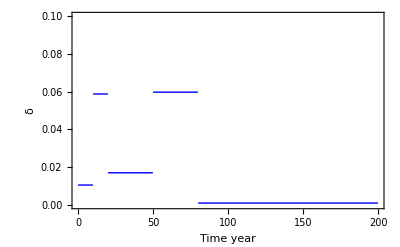

```mathematica
(*Plot instantaneous rate of transition to AI (Problem: some negative values!)*)
Plot[δP,{t,0,200}, Frame->True, FrameLabel->{Time (year), δ}, LabelStyle->{FontSize->18,FontFamily->"Times", ,Black,Bold}, PlotStyle->{Blue,Thick}, PlotRange->{0, 0.1}]
```

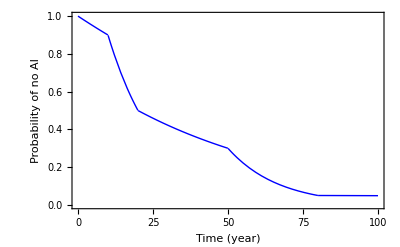

```mathematica
(*Plot probability of no AI over the next 100 years given timelines*)
Plot[pSurvive, {t,0,100},PlotRange->{{0,100},{0,1}}, Frame->True, FrameLabel->{"Time (year)", "Probability of no AI"} ,LabelStyle->{FontSize->18,FontFamily->"Times", ,Black,Bold}, PlotStyle->{Blue,Thick}]
```